GEOMETRICKÁ TRANSFORMÁCIA TROJUHOLNÍKA

==========================================

POČIATOČNÝ TROJUHOLNÍK:

Vrcholy trojuholníka ABC:

(-2 | 1
2 | 2
1 | 3)

Vlastnosti trojuholníka:

Obsah: 2

Obvod: 9

VYBRANÁ TRANSFORMÁCIA: Zväčšenie/Zmenšenie

GEOMETRICKÉ TRANSFORMÁCIE TROJUHOLNÍKA - ZVÄČŠENIE/ZMENŠENIE

========================================

ZADANIE:

Majme trojuholník ABC s vrcholmi:

(-2 | 1
2 | 2
1 | 3)

Vykonajte zmenšenie v smere osi x trojuholníka pomocou transformačnej matice v 2D priestore:

(1/2 | 0
0 | 1)

POSTUP:

Pre výpočet použijeme maticu zmenšenie v smere osi x v tvare:

Transformačná matica:

(sx | 0
0 | sy)

kde:

sx je koeficient zmenšenie v smere osi x v smere osi x

sy je koeficient zmenšenie v smere osi x v smere osi y

V našom prípade:

sx = 1/2 (zmenšovanie v smere osi x)

sy = 1 (zmenšovanie v smere osi y)

Výpočet pre jednotlivé vrcholy:

Vrchol A:

Pôvodné súradnice: [-2, 1]

Výpočet x-ovej súradnice:

x' = sx · x = 1/2 · -2

x' = -1

x' = -1

Výpočet y-ovej súradnice:

y' = sy · y = 1 · 1

y' = 1

Výsledné súradnice: [-1, 1]

Overenie pomocou inverznej transformácie:

x = x'/sx = -1/1/2 = -2

y = y'/sy = 1/1 = 1

Maticový zápis:

(1/2 | 0
0 | 1) · (-2
1) = (-1
1)

Vrchol B:

Pôvodné súradnice: [2, 2]

Výpočet x-ovej súradnice:

x' = sx · x = 1/2 · 2

x' = 1

x' = 1

Výpočet y-ovej súradnice:

y' = sy · y = 1 · 2

y' = 2

Výsledné súradnice: [1, 2]

Overenie pomocou inverznej transformácie:

x = x'/sx = 1/1/2 = 2

y = y'/sy = 2/1 = 2

Maticový zápis:

(1/2 | 0
0 | 1) · (2
2) = (1
2)

Vrchol C:

Pôvodné súradnice: [1, 3]

Výpočet x-ovej súradnice:

x' = sx · x = 1/2 · 1

x' = 1/2

x' = 1/2

Výpočet y-ovej súradnice:

y' = sy · y = 1 · 3

y' = 3

Výsledné súradnice: [1/2, 3]

Overenie pomocou inverznej transformácie:

x = x'/sx = 1/2/1/2 = 1

y = y'/sy = 3/1 = 3

Maticový zápis:

(1/2 | 0
0 | 1) · (1
3) = (1/2
3)

VÝSLEDOK:

Vrcholy trojuholníka po zmenšenie v smere osi x:

(-1 | 1
1 | 2
1/2 | 3)

VIZUALIZÁCIA:

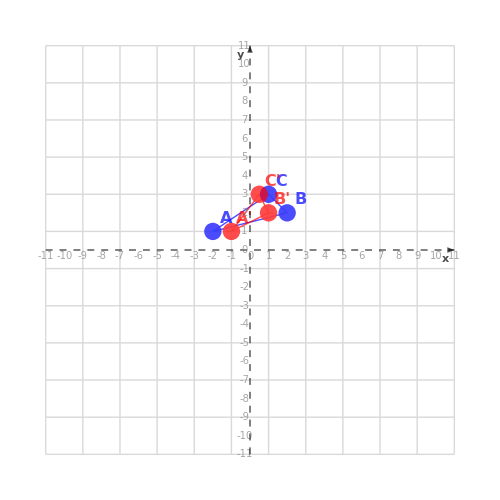

LEGENDA:

• Modré body a čiary: Pôvodný trojuholník

• Červené body a čiary: Trojuholník po zmenšenie v smere osi x

• Zelené prerušované čiary: Dráha zmeny veľkosti vrcholov

• Mriežka: Súradnicový systém

Pôvodné vrcholy (modrá):

Vrchol A: {-2,1}

Vrchol B: {2,2}

Vrchol C: {1,3}

Výsledné vrcholy (červená):

Vrchol A': {-1,1}

Vrchol B': {1,2}

Vrchol C': {1/2,3}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite koeficienty:

sx' = 1/sx = 2 (zväčšovanie v smere osi x)

sy' = 1/sy = 1 (zmenšovanie v smere osi y)

MATEMATICKÉ VLASTNOSTI:

• Pri rôznych koeficientoch (sx = 1/2, sy = 1):

- Mení sa tvar (podobnosť) geometrických útvarov

- Uhly medzi úsečkami sa menia

- Pomer dĺžok úsečiek sa mení v závislosti od ich smeru

- Obsah trojuholníka sa zmenší na 2. časť

• Nemení sa poloha počiatku súradnicovej sústavy [0,0]

• Body, ktoré ležia na osi x, zostanú ležať na osi x (ich y-ová súradnica zostáva nulová)

• Body, ktoré ležia na osi y, zostanú ležať na osi y (ich x-ová súradnica zostáva nulová)

VÝSLEDOK TRANSFORMÁCIE:

Pôvodný trojuholník ABC:

Vrcholy:

(-2 | 1
2 | 2
1 | 3)

Vlastnosti trojuholníka:

Obsah: 2

Obvod: 9

Po transformácii (Zväčšenie/Zmenšenie):

Vrcholy trojuholníka A'B'C':

(-1 | 1
1 | 2
1/2 | 3)

Vlastnosti trojuholníka:

Obsah: 1

Obvod: 6

VIZUALIZÁCIA TRANSFORMÁCIE:

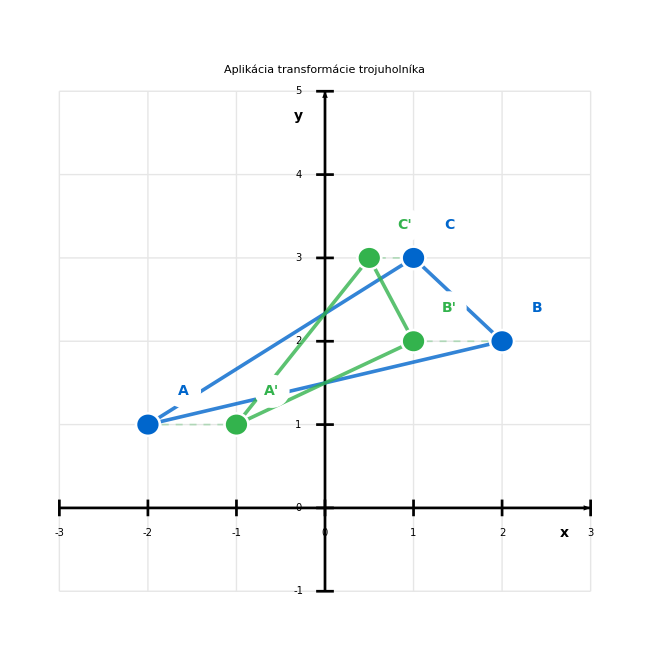

LEGENDA:

• Modré body a čiary: Pôvodný trojuholník ABC

• Zelené body a čiary: Trojuholník A'B'C' po transformácii (Zväčšenie/Zmenšenie)

{{{-2,1},{2,2},{1,3}},{{-1,1},{1,2},{1/2,3}},Zväčšenie/Zmenšenie}

```mathematica
TrojuholnikJednaTransformacia[]
```